```mathematica
(* EA Af NA SA An Au *)
```

```mathematica
l={54*^6,
30*^6,
24*^6,
18*^6,
14*^6,
76*^5,
(* Gl NG Bo Md BI Sm *)
22*^5,
79*^4,
74*^4,
59*^4,
51*^4,
44*^4,
(* Ho VI GB EI Sw SI Jv NI *)
23*^4,
22*^4,
21*^4,
20*^4,
18*^4,
15*^4,
14*^4,
112000
};
```

```mathematica
N[l]
```

{5.4×10^7,3.×10^7,2.4×10^7,1.8×10^7,1.4×10^7,9.×10^6,2.1×10^6,790000.,740000.,590000.,510000.,440000.,230000.,220000.,210000.}

```mathematica
Differences[Log[N[l]]]
```

{-0.587787,-0.223144,-0.287682,-0.251314,-0.441833,-1.45529,-0.97766,-0.0653828,-0.226528,-0.145712,-0.147636,-0.648695,-0.0444518,-0.04652}

```mathematica
?ConstantArray
```

ConstantArray[c,n] generates a list of n copies of the element c.
ConstantArray[c,{n_1,n_2,…}] generates an n_1×n_2×… array of nested lists containing copies of the element c.

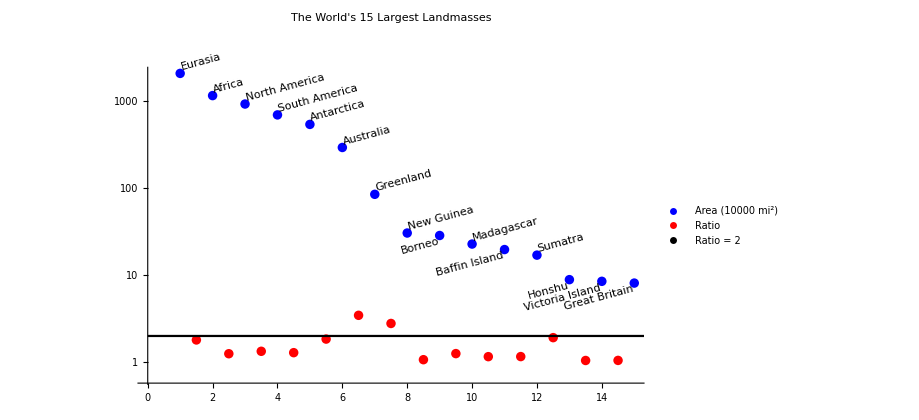

```mathematica
Show[ListLogPlot[{MapThread[Labeled,{l[[;;15]]/25899.88,Map[Rotate[#,15 Degree]&,{"Eurasia","Africa","North America","South America","Antarctica","Australia","Greenland","New Guinea","Borneo","Madagascar","Baffin Island","Sumatra","Honshu","Victoria Island","Great Britain"}]}],Transpose@{Range[1.5,15],Exp[-Differences[Log[l[[;;15]]]]]},{{}}},PlotStyle->{{Blue,PointSize[0.01]},{Red,PointSize[0.01]},{Black,PointSize[0.01]}},PlotLegends->Placed[{"Area (10000 mi^2)","Ratio","Ratio = 2"},{Right,Top}],PlotLabel->"The World's 15 Largest Landmasses"],LogPlot[2,{x,0,20},PlotStyle->Black]]
```

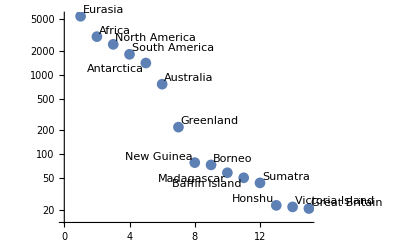

```mathematica
ListLogPlot[MapThread[Labeled,{l[[;;15]]/10^4,{"Eurasia","Africa","North America","South America","Antarctica","Australia","Greenland","New Guinea","Borneo","Madagascar","Baffin Island","Sumatra","Honshu","Victoria Island","Great Britain"}}]]
```

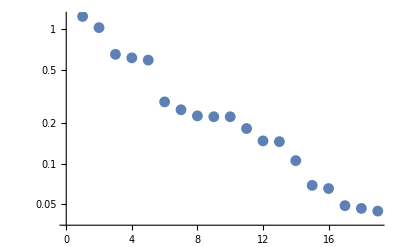

```mathematica
ListLogPlot[-Sort[Differences[Log[N@l]]]]
```